Electron Driven PWFA Blowout Radius Analysis
Audrey Farrell

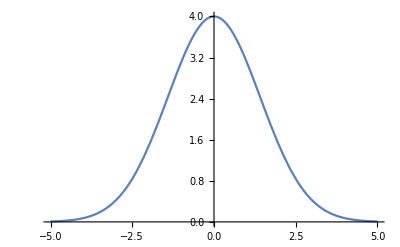

NMaximize::nnum: The function value -r[-0.829053] is not a number at {xi} = {-0.829053}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

NDSolve::overdet: There are fewer dependent variables, {r[xi]}, than equations, so the system is overdetermined.

NDSolve[{1/4 r[xi] (1+1/((1+1/4 (-1+(Log[1+(1+0.1 r[xi])/r[xi]]^2 (1+(1+0.1 r[xi])/r[xi])^2)/(-1+(1+(1+0.1 r[xi])/r[xi])^2)) r[xi]^2)^2))+r[xi] (1/2+3/4 (-1+(Log[1+(1+0.1 r[xi])/r[xi]]^2 (1+(1+0.1 r[xi])/r[xi])^2)/(-1+(1+(1+0.1 r[xi])/r[xi])^2))+3/4 ((2 Log[1+(1+0.1 r[xi])/r[xi]] (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi]) (1+(1+0.1 r[xi])/r[xi]))/(-1+(1+(1+0.1 r[xi])/r[xi])^2)+(2 Log[1+(1+0.1 r[xi])/r[xi]]^2 (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi]) (1+(1+0.1 r[xi])/r[xi]))/(-1+(1+(1+0.1 r[xi])/r[xi])^2)-(2 Log[1+(1+0.1 r[xi])/r[xi]]^2 (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi]) (1+(1+0.1 r[xi])/r[xi])^3)/((-1+(1+(1+0.1 r[xi])/r[xi])^2)^2)) r[xi]+1/8 ((Log[1+(1+0.1 r[xi])/r[xi]]^2 (2 (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi])^2+2 ((2 (1+0.1 r[xi]))/r[xi]^3-0.2/r[xi]^2) (1+(1+0.1 r[xi])/r[xi])))/(-1+(1+(1+0.1 r[xi])/r[xi])^2)+4 ((2 Log[1+(1+0.1 r[xi])/r[xi]] (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi]))/((-1+(1+(1+0.1 r[xi])/r[xi])^2) (1+(1+0.1 r[xi])/r[xi]))-(2 Log[1+(1+0.1 r[xi])/r[xi]]^2 (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi]) (1+(1+0.1 r[xi])/r[xi]))/((-1+(1+(1+0.1 r[xi])/r[xi])^2)^2)) (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi]) (1+(1+0.1 r[xi])/r[xi])+(1/(-1+(1+(1+0.1 r[xi])/r[xi])^2)((2 (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi])^2)/(1+(1+0.1 r[xi])/r[xi])^2-(2 Log[1+(1+0.1 r[xi])/r[xi]] (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi])^2)/(1+(1+0.1 r[xi])/r[xi])^2+(2 Log[1+(1+0.1 r[xi])/r[xi]] ((2 (1+0.1 r[xi]))/r[xi]^3-0.2/r[xi]^2))/(1+(1+0.1 r[xi])/r[xi]))+Log[1+(1+0.1 r[xi])/r[xi]]^2 (-(2 (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi])^2)/((-1+(1+(1+0.1 r[xi])/r[xi])^2)^2)-(2 ((2 (1+0.1 r[xi]))/r[xi]^3-0.2/r[xi]^2) (1+(1+0.1 r[xi])/r[xi]))/((-1+(1+(1+0.1 r[xi])/r[xi])^2)^2)+(8 (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi])^2 (1+(1+0.1 r[xi])/r[xi])^2)/((-1+(1+(1+0.1 r[xi])/r[xi])^2)^3))-(8 Log[1+(1+0.1 r[xi])/r[xi]] (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi])^2)/((-1+(1+(1+0.1 r[xi])/r[xi])^2)^2)) (1+(1+0.1 r[xi])/r[xi])^2) r[xi]^2) r'[xi]^2+(1+r[xi]^2 (1/4+1/2 (-1+(Log[1+(1+0.1 r[xi])/r[xi]]^2 (1+(1+0.1 r[xi])/r[xi])^2)/(-1+(1+(1+0.1 r[xi])/r[xi])^2))+1/8 ((2 Log[1+(1+0.1 r[xi])/r[xi]] (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi]) (1+(1+0.1 r[xi])/r[xi]))/(-1+(1+(1+0.1 r[xi])/r[xi])^2)+(2 Log[1+(1+0.1 r[xi])/r[xi]]^2 (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi]) (1+(1+0.1 r[xi])/r[xi]))/(-1+(1+(1+0.1 r[xi])/r[xi])^2)-(2 Log[1+(1+0.1 r[xi])/r[xi]]^2 (-(1+0.1 r[xi])/r[xi]^2+0.1/r[xi]) (1+(1+0.1 r[xi])/r[xi])^3)/((-1+(1+(1+0.1 r[xi])/r[xi])^2)^2)) r[xi])) r''[xi]==λ[4]/r[xi],r[xi]==4,r[3 √2]==0},r[xi],xi]

```mathematica
rmax = 4;
delta=1 + 0.1 r[xi];
σr = 0.1;
σz = Sqrt[2];

a= delta/r[xi];
β= (1+a)^2 Log[(1+a)]^2  / ((1+a)^2 - 1) - 1;

Aeq= 1 + (1/4 + β/2 + 1/8 * r[xi] * D[β,r [xi]])r[xi]^2;
Beq= 1/2 + 3 β/4 + 3/4 r[xi] D[β,r[xi]] + 1/8 r[xi]^2 D[β,{r[xi],2}];
Ceq= 1/4 (1 + 1/(1+ β/4 r[xi]^2)^2);

Eq= Aeq D[r[xi],{xi,2}] + Beq r[xi] (D[r[xi],xi])^2 + Ceq r[xi];

nb0[rmax_]:= rmax^2/(4 σr^2);
Int[r_]:= Quiet@Integrate[rp  Exp[-rp^2/(2*σr^2)], rp]/.rp-> r
λ[rmax_,xi_]:=Quiet@(Exp[-xi^2/(2*σz^2)]* nb0[rmax]*(Int[100*σr] -Int[0]));

Plot[λ[rmax,xi],{xi,-5,5}]
xiMin = 3*σz;
rb= NDSolve[{Eq== λ[rmax]/r[xi],NMaximize[r[xi],xi][[1]] == rmax, r[xiMin]==0}, r[xi],xi];
Print[rb]
```